-(ⅈ (-ⅈ Rs+L ω))/(-1-ⅈ Cp Rs ω+Cp L ω^2)

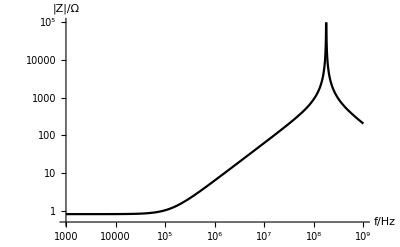

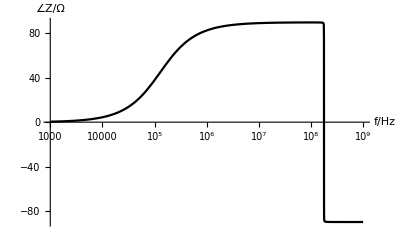

```mathematica
ClearAll[Cp,L,Rs];
Par[x_,y_]:=(x y)/(x+y);
Z[ω_]:=Par[ⅈ ω L+Rs,1/(ⅈ ω Cp)];
(*Z[ω_]:=Par[Rs+ⅈ ω L,1/(ⅈ ω Cp)];*)
Factor[Z[ω]]
L=1*10^-6;Rs=0.81;Cp=0.8*10^-12;(*coilcraft 0603LS-102X_E_*)
LogLogPlot[Abs[Z[2 π f]],{f,10^3,10^9},PlotRange->{.5,10^5},PlotTheme->"Monochrome",AxesLabel->{"f/Hz","|Z|/Ω"}]
LogLinearPlot[Arg[Z[2 π f]]*180/π,{f,10^3,10^9},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"f/Hz","∠Z/Ω"}]
```

```mathematica
ClearAll[Cp,L,Rs];
fac=-1+ⅈ Cp Rs ω+Cp L ω^2;
num=(-ⅈ (-ⅈ Rs+L ω))*fac;
den=(-1-ⅈ Cp Rs ω+Cp L ω^2)*fac;
Expand[num]
Expand[den]
```

Rs+ⅈ L ω-ⅈ Cp Rs^2 ω-ⅈ Cp L^2 ω^3

1-2 Cp L ω^2+Cp^2 Rs^2 ω^2+Cp^2 L^2 ω^4

```mathematica
ClearAll[L,C,x]
Solve[(1-L C x^2)^2+R^2 C^2 x^2==0,x]
```

{{x→-(√(2/(C L)-R^2/L^2-(R √(-4 L+C R^2))/(√C L^2)))/(√2)},{x→(√(2/(C L)-R^2/L^2-(R √(-4 L+C R^2))/(√C L^2)))/(√2)},{x→-√(1/(C L)-R^2/(2 L^2)+(R √(-4 L+C R^2))/(2 √C L^2))},{x→√(1/(C L)-R^2/(2 L^2)+(R √(-4 L+C R^2))/(2 √C L^2))}}

```mathematica
(*(ⅈ (-ⅈ Rs+L ω))/(1+ⅈ Cp Rs ω-Cp L ω^2)*)
ClearAll[Cp,L,Rs];
num=ⅈ (-ⅈ Rs+L ω);
den=1+ⅈ Cp Rs ω-Cp L ω^2;
Simplify[Expand[num]]
Expand[den]
```

Rs+ⅈ L ω

1+ⅈ Cp Rs ω-Cp L ω^2

```mathematica
ComplexExpand[(ⅈ (-ⅈ Rs+L ω))/(1+ⅈ Cp Rs ω-Cp L ω^2)]
```

Rs/(Cp^2 Rs^2 ω^2+(1-Cp L ω^2)^2)+ⅈ ((L ω)/(Cp^2 Rs^2 ω^2+(1-Cp L ω^2)^2)-(Cp Rs^2 ω)/(Cp^2 Rs^2 ω^2+(1-Cp L ω^2)^2)-(Cp L^2 ω^3)/(Cp^2 Rs^2 ω^2+(1-Cp L ω^2)^2))